# A new chiral 4-polytope

Starry from convex

## BookChapterNumber.Section. Summary

In this chapter we show how to construct the regular starry 4-polytope {5/2,3,5} “Great stellated 120-cell” from the regular convex 600-cell {3,3,5}. The construction is based on the observation that, in the same way as the false vertices of a pentagram form a pentagon, the false vertices of a great stellated dodecahedron {5/2,3} form an icosahedron.

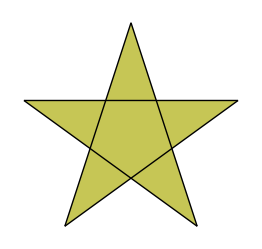
-Graphics--Graphics3D-

This icosahedron is thought to be the vertex figure of some vertex in {3,3,5}, so that its center and its vertices represent some vertices of {3,3,5}. We choose a basic flag for this icosahedron, which determines the generating reflections R_0 to R_3 of the symmetry group [3,3,5]. Then we choose a base flag in the surrounding {5/2,3}, which determines reflections P_0 to P_3. We may express the P_i in terms of the R_i. Acting with the group generated by the P_i on the base flag of  {5/2,3} will generate {5/2,3,5}.

## BookChapterNumber.Section. From second to third dimension

For better understanding, we start by presenting the 2-dimensional analogue of our argument. Take the pentagon of false-vertices of the pentagram to be the vertex-figure of some vertex in a regular icosahedron:

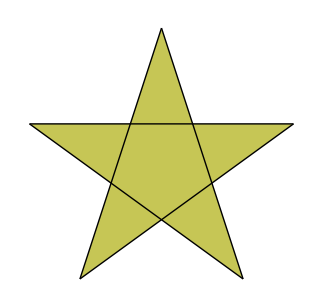
-Graphics--Graphics3D-f

Choose a flag that will generate the whole icosahedron, and think of how it should look in the 2-dimensional picture:

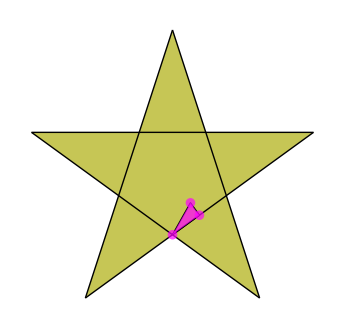
-Graphics--Graphics3D-

Let R_i for i=0,1,2 be reflections on the sides of this magenta triangle in the following way: R_0 goes through the blue and green vertex, R_1through the red and blue, and R_2 through the red and green. Notice these line reflections correspond to plane reflections on three of the four the sides of the magenta tetrahedron in the 3D picture.

Now choose a flag that will generate the pentagram in the 2-dimensional picture:

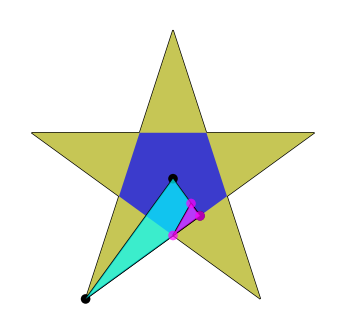

Define the reflections P_i on the sides of the cyan triangle in terms of the R_i. We should choose

P_0=R_0,   P_1=R_1 R_2 R_1 R_0 R_1 R_2 R_1, and   P_2=R_2

P_1 is just conjugating R_0 by the reflection through vertical line in the center of the picture.

Just like before, we may think the P_i are plane reflections in the icosahedron. This produces a base flag, which we color in cyan:

-Graphics3D-

And we act on the cyan flag with the group generated by the P_i:

-Graphics3D-

It’s {5/2,5}! A regular star polyhedron with the same vertex-set as the icosahedron.

## BookChapterNumber.Section. From third to fourth dimension

Now let’s construct {5/2,3,5} from {3,3,5}. We start with a regular icosahedron and imagine it’s the vertex figure of some vertex in {3,3,5}. Then we choose a basic flag. Recall that the cells are tetrahedra.

-Graphics3D--Graphics3D-

Left: the icosahedron as the vertex figure of some vertex that is not in the base flag. Right: the base flag within the base cell.

And now choose a base flag for the {5/2,3}:

-Graphics3D-

Basic flag of {5/2,3}. We highlight the edges of the base face.

Notice the relation between the two flags:

-Graphics3D--Graphics3D-

Left: the two base flags. Right: the two base flags within the two base cells.

Now we find expressions for the reflections associated with each flag. For the base flag of {3,3,5}, colored in pink, define the red vertex as v_0, the blue v_1, the green v_3 and the yellow v_4. The mirror of the reflection R_i is the plane through all but v_i.

For example, R_0 is a reflection with respect to the following plane:

-Graphics3D-

Recall we will think of these as hyperplane reflections, determined by the three vertices in the base flag and the origin in 4-space.

Now we express the P_i in terms of the R_i. There’s three easy relations:

-Graphics3D-

R_0=P_0

-Graphics3D-

R_3=P_2

-Graphics3D-

R_2=P_3

Finding P_1 is done by conjugating R_0 by R_1 R_2 R_3 R_2 R_1:

-Graphics3D--Graphics3D-

The plane of reflection of R_0 after conjugating by R_1 R_2 R_3 R_2 R_1

So we define

P_1=R_1 R_2 R_3 R_2 R_1 R_0 R_1 R_2 R_3 R_2 R_1

That’s all the relations we were looking for.

Now we should make sure these are, in fact, generators of the group [5/2,3,5]. The following properties can be checked before considering the geometric representation of the groups:

(P_0 P_1)^5=(P_1 P_2)^3=(P_2 P_3)^5=Id

(P_0 P_2)^2=(P_0 P_3)^2=(P_1 P_3)^2=Id

The intersection property was confirmed in GAP.

Next we must make sure the construction can be used to construct a faithful and symmetric realization of {5/2,3,5}. For this we first need to choose a base vertex and act on it with the P_i as in Wythoff’s construction. This vertex should be fixed by P_1, P_2 and P_3 but not by P_0. We take the following vertex from {3,3,5}:

-Graphics3D--Graphics3D-

Base vertex of the {5/2,3,5} highlighted in magenta. The point lies in the plane P_1.

It has been computed that for the choice of basic flag of {3,3,5}

v_0=(1,0,0,0), v_1=(2+ρ,1,0,1-ρ), v_2=(ρ,ρ^-1,0,0), v_3=(ρ^2,1,-ρ^-1,0)

the base vertex of {5/2,3,5} is

w_0=(ρ/2,-1/2,0,1/2-ρ/2)

Faithfulness and symmetry of the realization are being shown in these days (with very little chance of error). We show (prototype) figures of the stereographic projection of the base cell and face of {5/2,3,5}.

-Graphics3D--Graphics3D-

(In progress) Left: stereographic projection of the base cell of {5/2,3,5}. Right: stereographic projection of the base face of  {5/2,3,5} and the base cell of  {3,3,5}. The base flag is included.

Chiral from starry

Now we define the isometries that upon action on the base vertex of the great stellated 120-cell produce a new chiral 4-polytope.

S_1=P_0 P_1 P_3 P_2

S_2=P_2 P_1

S_3=P_3 P_2

S_2 and S_3 are rotations about the vertex and edge of the basic flag of {5/2,5,3}. S_1 is an order-12 twist. Define the basic edge e to be the segment from the basic vertex w_0 to w_0 S_1^-1=w_0 P_0, the basic face f to be the cycle w_0⟨S_1⟩ and the basic cell c to be f⟨S_1,S_2⟩. The structure c⟨S_1,S_2,S_3⟩ is a chiral 4-polytope.

-Graphics3D-

(In progress) Stereographic projection of the basic face. The basic flag and face of {5/2,3,5} are also shown for reference.

The following relations hold:

(S_1 S_2)^2=Id

(S_1 S_2 S_3)^2=Id

w_0 S_3=w_0

e S_3=e

And the intersection property, which follows from

⟨S_1∩S_2⟩={Id}=⟨S_2∩S_3⟩   and   ⟨S_1∩S_2⟩∩⟨S_2∩S_3⟩ =⟨S_2⟩

Moreover, it has been computed that for the realization used in the previous section, we have

Stab_⟨S_1, S_2⟩w_0=⟨S_2⟩, Stab_⟨S_1, S_2⟩e=⟨S_1 S_2⟩ ,  Stab_⟨S_1, S_2⟩f=⟨S_1⟩ ,

Stab_⟨S_1, S_2, S_3⟩v=⟨S_2,S_3⟩,Stab_⟨S_1, S_2, S_3⟩e=⟨S_1 S_2,S_3⟩,   Stab_⟨S_1, S_2, S_3⟩f=⟨S_1,S_2 S_3⟩,   Stab_⟨S_1, S_2, S_3⟩c=⟨S_1,S_2⟩

From which it follows that every face is only in two cells. Other conditions for this to be a geometric skeletal polyope follow from the fact that the facets are copies of H_1({5,3,5/2}), as well as chirality.

The basic cell has 12 copies of that helical face. Here are five of them:

-Graphics3D-

Chiral from the dual starry

We may generate the dual star 4-polytope {5,3,5/2} by simply defining

Q_0=P_3, Q_1=P_2, Q_2=P_1 and Q_3=P_0

and using for a base vertex the center of a cell from the dual {5/2,3,5}.

It turns out the same relations hold and have another chiral polytope! Here’s the basic face:

-Graphics3D-

(In progress) Stereographic projection of the basic face of the chiral 4-polytope obtain from {5,3,5/2}. The basic flag and face of  {5,3,5/2} are shown for reference.

And eight of the twelve faces in the base cell:

-Graphics3D-